DSolve::overdet: There are fewer dependent variables than equations, so the system is overdetermined.

Set::shape: Lists {r[t_],ang[t_],ang2[t_]} and {epsilon''[t]==653.333-9 theta[t]+3 theta2[t],theta''[t]==0.+3 (1-3 epsilon[t]),theta2''[t]==0.+13.5 (-1+3 epsilon[t]),25.5604 theta2[t] theta2'[t]==0,epsilon[0]==0,theta[0]==0,theta2[0]==0,epsilon'[0]==0,theta'[0]==0,theta2'[0]==0} are not the same shape.

{epsilon''[t]==653.333-9 theta[t]+3 theta2[t],theta''[t]==0.+3 (1-3 epsilon[t]),theta2''[t]==0.+13.5 (-1+3 epsilon[t]),25.5604 theta2[t] theta2'[t]==0,epsilon[0]==0,theta[0]==0,theta2[0]==0,epsilon'[0]==0,theta'[0]==0,theta2'[0]==0}

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

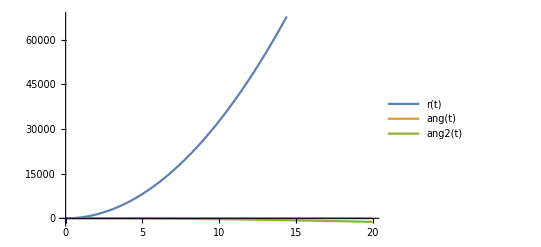

```mathematica
a:=0.015
A:=1
M:=0.0075
i1:=M*(0.01)^2/6
i3:=i1
g:=9.8
m2:=0.00001
B:=0
omega:=Sqrt[g/a]
alpha:=0
beta:=Pi/2
{r[t_],ang[t_],ang2[t_]}=First[DSolve[{
epsilon''[t]==3*A*Sin[beta]*theta2[t]-9*A*Cos[alpha]*theta[t]+g/a,
theta''[t]==theta[t]*(omega^2-g/a)+3*A*Cos[alpha]*(1-3*epsilon[t]),
theta2''[t]==theta2[t]*(omega^2-omega^2*i3/i1-m2*B/i1)+A*a^2*M*Sin[beta]*(3*epsilon[t]-1)/i1,
omega*theta2[t]*theta2'[t]==0,
epsilon[0]==0,theta[0]==0,theta2[0]==0,epsilon'[0]==0,theta'[0]==0,theta2'[0]==0},
{epsilon[t],theta[t],theta2[t]},t]]
Plot[{r[t],ang[t],ang2[t]},{t,0,20},PlotLegends->"Expressions"]
```

```mathematica
MatrixForm[MatrixPower[{{0,-9*A*Cos[alpha]},{i,0}},1/2]]
```

((0.5+0. ⅈ) √((0.-0.003 ⅈ) √i)+(0.5+0. ⅈ) √((0.+0.003 ⅈ) √i) | -((0.+0.0015 ⅈ) √((0.-0.003 ⅈ) √i))/(√i)+((0.+0.0015 ⅈ) √((0.+0.003 ⅈ) √i))/(√i)
(0.+166.667 ⅈ) √((0.-0.003 ⅈ) √i) √i-(0.+166.667 ⅈ) √((0.+0.003 ⅈ) √i) √i | (0.5+0. ⅈ) √((0.-0.003 ⅈ) √i)+(0.5+0. ⅈ) √((0.+0.003 ⅈ) √i))

```mathematica
{ry[t_],ang2y[t_]}=Values[First[NDSolve[{
epsilon''[t]==-3*A*Sin[beta]*theta2[t]+g/a,
theta2''[t]==theta2[t]*g/a+A*a^2*M*Sin[beta]*(1-3*epsilon[t])/i1,
epsilon[0]==1/3,theta2[0]==Sqrt[2]/9,epsilon'[0]==0,theta2'[0]==0},
{epsilon[t],theta2[t]},{t,0,1}]]];
Plot[{ry[t],ang2y[t]},{t,0,1},PlotLegends->"Expressions"]
```

General::munfl: 1/(5.02163×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.02245×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.84878×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
NSolve[{
-1000000*epsilon==-3*A*Sin[beta]*theta2-9*A*Cos[alpha]*theta+g/a,
-theta==theta*(omega^2-g/a)+3*A*Cos[alpha]*(1-3*epsilon),
-theta2==theta2*omega^2+A*a^2*M*Sin[beta]*(1-3*epsilon)/i1},
{epsilon,theta,theta2}]
```

{{epsilon→-0.0098,theta→0.,theta2→-2.10082×10^-20}}

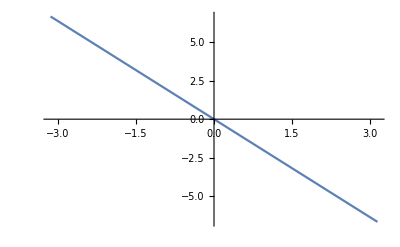

```mathematica
Plot[-3*A*Sin[beta]*theta2-9*A*Cos[alpha]*Sqrt[2]/9+g/a,{theta2,-Pi,Pi}]
```